# Poisson problem - High gradient with Arc Tan

## Global variables

```mathematica
(*Clear[KValue]
KValue=10000;*)
Clear[F]
F[Kv_]:= 2Sqrt[Kv];
```

## One dimensional problem - Solution

```mathematica
Clear[a,r,P]
r=0.25;
a=0.5;
P=2./Pi;
Coeff = -2.;
arc[x_,Kv_]:= F[Kv]*(r^2- (x-a)*(x-a));
prodx[x_]:=x*(x-1.);
Sol1D[x_,Kv_]:=Coeff*prodx[x]*(1.+P*ArcTan[arc[x,Kv]])
```

```mathematica
DSol1D[x_,Kv_]:=Simplify[D[Sol1D[x,Kv],x]]
```

SetDelayed::write: Tag Plus in (2.`  - 16.` « 3 » « 1 » « 1 » « 1 » + 5.092958178940651` √Kv (-1.` + x) (-0.5` + x) x/1.`  + 4.` Kv (-0.75` + x)^2 (-0.25` + x)^2 + (-1.2732395447351628` + « 1 ») « 1 »)[« 1 »] is Protected.

$Failed

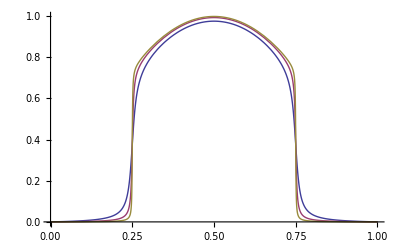

```mathematica
Plot[{Sol1D[x,10000],Sol1D[x,100000],Sol1D[x,1000000]},{x,0,1.},AxesOrigin->{0.,0.}]
```

```mathematica
YLinha[x_]:=(Coeff/Pi)*(1-2 x)*(Pi+(2.*ArcTan[arc[x]])+4*Sqrt[KValue]*(prodx[x]/(1.+arc[x]*arc[x])))
```

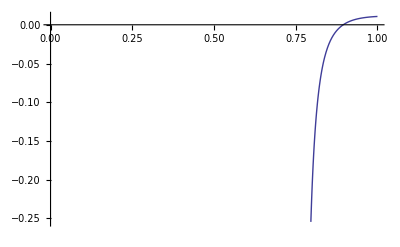

```mathematica
Plot[YLinha[x],{x,0.78,1},AxesOrigin->{0.,0.}]
```

```mathematica
Clear[Diferenca]
Diferenca[x_]:=Simplify[Expand[DSol1D[x]-YLinha[x]]]
```

```mathematica
Diferenca[0.1]
```

## Two Dimensional problem - Solution

```mathematica
Coeff = 8.;
arc[x_,y_,Kv_]:= F[Kv]*((0.25)^2 - (x-0.5)^2- (y-0.5)^2);
prod[x_]:=x*(x-1.);
Sol2D[x_,y_,Kv_]:=Coeff*prod[x]*prod[y]*(1.+(2./Pi)*ArcTan[arc[x,y,Kv]])
```

```mathematica
Plot3D[Sol2D[x,y,100000],{x,0.,1.},{y,0.,1.}]
```

-Graphics3D-

## Three Dimensional problem - Solution

```mathematica
Clear[arc,prod,Coeff]
Coeff = -32.;
arc[x_,y_,z_,Kv_]:= F[Kv]*((0.25)^2 - (x-0.5)^2- (y-0.5)^2- (z-0.5)^2);
prod[x_]:=x*(x-1.);
Sol3D[x_,y_,z_,Kv_]:=Coeff*prod[x]*prod[y]*prod[z]*(1.+(2./Pi)*ArcTan[arc[x,y,z,Kv]])
```

```mathematica
Sol3D[0.5,0.5,0.5,100000]
```

0.991949

```mathematica
RegionPlot3D[Sol3D[x,y,z,100000]>.9,{x,0,1},{y,0,1},{z,0,1}]
```

-Graphics3D-